```mathematica
ClearAll["Global`*"]
```

```mathematica
m[alpha_]:=2^(1/3)Pi^2((AiryAi[-2^(2/3)alpha])^2+(AiryBi[-2^(2/3)alpha])^2); (*scaling function M(alpha), see Eq. 44 in SI*)
```

```mathematica
R[alpha_]:=Pi NIntegrate[r Erfc[r^3/Sqrt[2] Sin[phi]Cos[phi]] Exp[-1/6 r^6(1/8 (5+3 Cos[4 phi]))-2 alpha r^2],{r,0,Infinity},{phi,0 ,Pi/2}]; (*scaling function R(alpha) = (M(alpha)^2-S(alpha))/8, so S(alpha) = M(alpha)^2-8 R(alpha), see Eq. 49 in the SI*)
```

# Compare model to Bullock & Diecke 1956

## Fig. 3 (spontaneous background firing) and resulting prediction of CV vs. frequency curve

```mathematica
(*import data from Fig. 3 of Bullock and Diecke (originally extracted with the help of WebPlotDigitizer): x value: interspike time in ms, y value: probability for interspike time to be in interval [0.9x, 1.1x]: normalized by 1/100 as compared to Fig. 3 in Bullock and Diecke*)list={{270.553,6.31849},{221.511,5.37671},{181.477,8.57877},{146.863,16.4897},{120.841,19.5034},{98.3991,11.5925},{80.5339,8.39041},{66.2328,8.39041},{53.7819,10.274},{44.0187,7.26027},{36.0214,3.11644}}; (*spontaneous background*)
list=Transpose[{Transpose[list][[1]],Transpose[list][[2]]/Total[Transpose[list][[2]]]}]; (*normalize probability*)
listhighI={{29.7502,2.36301},{24.2454,27.226},{19.8925,67.1575},{16.342,5.18836}};(*I=64, initial plateau*)
listhighI=Transpose[{Transpose[listhighI][[1]],Transpose[listhighI][[2]]/Total[Transpose[listhighI][[2]]]}]; (*normalize probability*)
listhighIFirstAdap={{53.7052,1.23288},{36.0332,5.18836},{29.8007,13.0993},{24.2591,58.3048},{19.9269,23.0822}}; (*I=64, after first adaptation*)
listhighIFirstAdap=Transpose[{Transpose[listhighIFirstAdap][[1]],Transpose[listhighIFirstAdap][[2]]/Total[Transpose[listhighIFirstAdap][[2]]]}];  (*normalize probability*)
listlowIFirstAdap={{181.272,1.42123},{147.265,6.31849},{120.69,11.5925},{98.8069,10.274},{80.625,15.5479},{65.7224,14.4178},{54.0853,18.3733},{44.2459,12.3459},{36.2245,11.2158},{29.8735,1.04452}}; (*I=8*)
listlowIFirstAdap=Transpose[{Transpose[listlowIFirstAdap][[1]],Transpose[listlowIFirstAdap][[2]]/Total[Transpose[listlowIFirstAdap][[2]]]}];  (*normalize probability*)
```

```mathematica
SampleSizeExp=100; (*in Bullock and Diecke 100 interspike times per condition are recorded*)
```

```mathematica
(*calculate the sample mean and sample variance for all four conditions*)
mean=Transpose[list][[1]].Transpose[list][[2]]; (*mean for spontaneous background*)
meanhighI=Transpose[listhighI][[1]].Transpose[listhighI][[2]];(*mean for I=64, initial plateau*)
meanhighIFirstAdap=Transpose[listhighIFirstAdap][[1]].Transpose[listhighIFirstAdap][[2]];(*mean for I=64, after first adaptation*)
meanlowIFirstAdap=Transpose[listlowIFirstAdap][[1]].Transpose[listlowIFirstAdap][[2]];(*mean for I=8*)
var=SampleSizeExp/(SampleSizeExp-1)((Transpose[list][[1]]*Transpose[list][[1]]).Transpose[list][[2]]-(Transpose[list][[1]].Transpose[list][[2]])^2);(*sample variance for spontaneous background*)
varhighI=SampleSizeExp/(SampleSizeExp-1)((Transpose[listhighI][[1]]*Transpose[listhighI][[1]]).Transpose[listhighI][[2]]-(Transpose[listhighI][[1]].Transpose[listhighI][[2]])^2);(*sample variance for I=64, initial plateau*)
varhighIFirstAdap=SampleSizeExp/(SampleSizeExp-1)((Transpose[listhighIFirstAdap][[1]]*Transpose[listhighIFirstAdap][[1]]).Transpose[listhighIFirstAdap][[2]]-(Transpose[listhighIFirstAdap][[1]].Transpose[listhighIFirstAdap][[2]])^2);(*sample variance for I=64, after first adaptation*)
varlowIFirstAdap=SampleSizeExp/(SampleSizeExp-1)((Transpose[listlowIFirstAdap][[1]]*Transpose[listlowIFirstAdap][[1]]).Transpose[listlowIFirstAdap][[2]]-(Transpose[listlowIFirstAdap][[1]].Transpose[listlowIFirstAdap][[2]])^2);(*sample variance for I=8*)
```

```mathematica
(*calculate the coefficient of variation for all four conditions*)
CV=Sqrt[var]/mean;
CVhighI=Sqrt[varhighI]/meanhighI;
CVhighIFirstAdap=Sqrt[varhighIFirstAdap]/meanhighIFirstAdap;
CVlowIFirstAdap=Sqrt[varlowIFirstAdap]/meanlowIFirstAdap;
```

```mathematica
(*calculate the mean frequency in Hz for all four conditions*)
frequency=1000/mean;
frequencyhighI=1000/meanhighI;
frequencyhighIFirstAdap=1000/meanhighIFirstAdap;
frequencylowIFirstAdap=1000/meanlowIFirstAdap;
```

```mathematica
(*determine the value of the scaling variable alpha at steady-state, alpha0, and the scaling time, taus, by matching the coefficient of variation and the mean frequency*)fitAlpha0Taus=FindRoot[{CV== Sqrt[1-8R[alpha0]/m[alpha0]^2],frequency==1/(tausfit m[alpha0])},{{alpha0,-0.24},{tausfit,0.013}}];
```

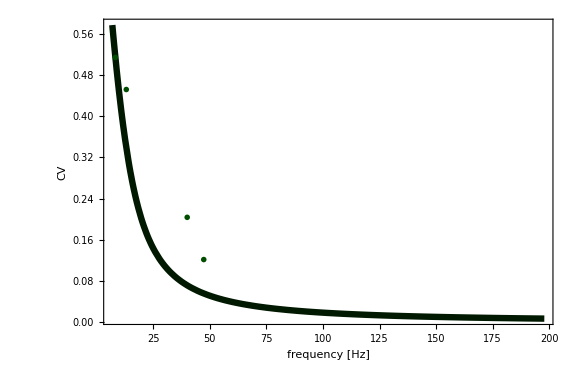

```mathematica
(*For inferred taus, plot theoretically expected CV versus frequency curve, together with the data for the four conditions*)
CVVsFrequencyComparisonPlot=Show[ParametricPlot[{1/((tausfit/.fitAlpha0Taus) m[x]),Sqrt[1-8R[x]/m[x]^2]},{x,0,200},PlotRange->All,FrameLabel->{"frequency [Hz]","CV"},Frame->True,PlotStyle->{Darker[Green,0.9],Thickness[0.008]}],ListPlot[{{frequency,CV},{frequencyhighI,CVhighI},{frequencyhighIFirstAdap,CVhighIFirstAdap},{frequencylowIFirstAdap,CVlowIFirstAdap}},PlotMarkers->{Automatic,Scaled[0.03]},PlotStyle->Darker[Green,0.7]],AxesOrigin->None,FrameStyle->Directive[22,Thick],ImageSize->Large,AspectRatio->2/3]
```

## Fig. 4 (temperature protocols)

```mathematica
(*import temperature data from Fig. 4 (originally extracted with the help of WebPlotDigitizer): x value: time (in s), y value: temperature diff (in K)*)TimeSeriesTemperature={{0.091283,0.0207922},{0.0315341,0.00662733},{0.0614147,0.013868},{0.115955,0.0264572},{0.152294,0.0343226},{0.205487,0.0453312},{0.246974,0.0531901},{0.346704,0.0695195},{0.472135,0.0848671},{0.629643,0.0976424},{0.786955,0.105355}}; (*upper curve*)
TimeSeriesTemperatureMiddle={{0.0365841,0.00408929},{0.067605,0.00753103},{0.102499,0.0112843},{0.130934,0.0144129},{0.160643,0.0172234},{0.191652,0.0203487},{0.220062,0.0228444},{0.24976,0.0253384},{0.291076,0.0287671},{0.362065,0.034057},{0.452371,0.0396389},{0.540054,0.0439583},{0.605798,0.0467232}}; (*middle curve*)
TimeSeriesTemperatureLower={{0.0558515,0.00311553},{0.0945452,0.00528174},{0.133239,0.00744795},{0.166773,0.00930424},{0.19772,0.0108473},{0.241562,0.013007},{0.278944,0.014542},{0.3189,0.0160737},{0.364016,0.0179153},{0.402673,0.0191322},{0.459372,0.0209592},{0.510898,0.0221598},{0.566285,0.0233555},{0.615226,0.0242429},{0.668027,0.0251254},{0.731124,0.0259949},{0.82382,0.026827}} ;(*lower curve*)
```

```mathematica
fit=FindFit[TimeSeriesTemperature,a(1- Exp[-b x]),{a,b},x];
fitMiddle=FindFit[TimeSeriesTemperatureMiddle,a(1- Exp[-b x]),{a,b},x];
fitLower=FindFit[TimeSeriesTemperatureLower,a(1- Exp[-b x]),{a,b},x];
```

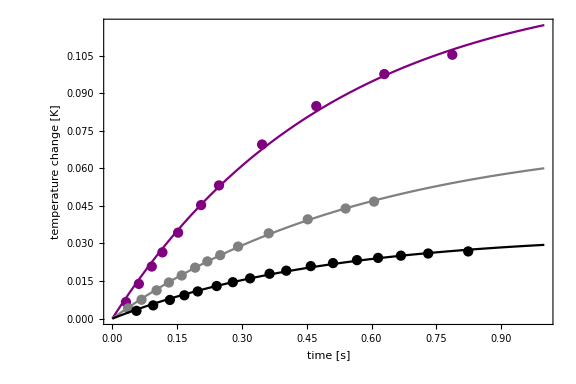

```mathematica
timecoursetemps=Show[ListPlot[{TimeSeriesTemperature,TimeSeriesTemperatureMiddle,TimeSeriesTemperatureLower},PlotStyle->{Purple,Gray,Black}],Plot[{a(1- Exp[-b x])/.fit,a(1- Exp[-b x])/.fitMiddle,a(1- Exp[-b x])/.fitLower},{x,0,1},PlotStyle->{Purple,Gray,Black}],PlotRange->All,
Frame->True,FrameLabel->{"time [s]","temperature change [K]"},FrameStyle->Directive[22,Thick],ImageSize->Large,AspectRatio->2/3]
```

## Fig. 4 (frequency time series and inference of additional parameters: k0 and a)

```mathematica
(*import time series frequency data from Fig. 4 (originally extracted with the help of WebPlotDigitizer): x value: time (in s), y value: frequency (in Hz)*)TimeSeriesFrequencyLong={{0.0164786,15.5202},{0.0331411,46.1603},{0.0554448,67.4936},{0.0814158,82.9851},{0.0968591,82.9297},{0.105771,76.0236},{0.11864,75.9813},{0.139405,88.7126},{0.130716,118.089},{0.18081,108.062},{0.189722,99.0631},{0.165396,35.0947},{0.276063,34.6259},{0.210419,108.862},{0.238829,118.559},{0.248921,98.8096},{0.226327,52.1229},{0.295812,51.5184},{0.309436,101.144},{0.323593,101.082},{0.332688,109.229},{0.344058,90.2437},{0.35445,98.3593},{0.373764,99.1315},{0.394365,99.9042},{0.414956,99.8152},{0.435547,99.7263},{0.453554,98.7898},{0.462679,109.56},{0.477638,71.0235},{0.488795,48.5041},{0.469965,234.608},{0.535618,238.028},{0.545507,165.405},{0.499874,97.7421},{0.51017,97.6986},{0.533277,92.6611},{0.556519,99.2055},{0.575823,99.1227},{0.569233,86.327},{0.600178,90.8074},{0.609293,99.8397},{0.620866,98.9296},{0.629787,91.4796},{0.642666,92.2235},{0.672256,91.3116},{0.682552,91.2709},{0.69785,80.1039},{0.713264,77.9984},{0.722553,100.215},{0.734126,99.3017},{0.744189,80.6384},{0.758336,79.8945},{0.809794,78.3485},{0.825286,81.7592},{0.83442,91.4612},{0.845887,82.3965},{0.859995,78.8581},{0.874044,71.6521},{0.885917,92.8513},{0.897364,82.2131},{0.910069,70.9239},{0.925638,79.318},{0.940781,60.6102},{0.976748,56.9579},{0.794361,25.0081}}; (*upper curve*)
```

```mathematica
TimeSeriesFrequencyLongMiddle={{0.0053316,22.9235},{0.025313,41.9819},{0.0497745,42.3021},{0.0884698,45.653},{0.102829,54.7201},{0.0697173,74.8354},{0.0646856,83.0452},{0.12225,60.6589},{0.137693,60.6183},{0.191173,36.2906},{0.158468,71.3908},{0.168899,80.5522},{0.199795,81.144},{0.211387,81.8084},{0.22296,81.0627},{0.234552,81.7264},{0.250431,120.569},{0.241722,157.74},{0.261442,72.3145},{0.275589,71.6473},{0.285884,71.6154},{0.298744,70.9587},{0.311613,70.9191},{0.341707,34.8279},{0.352805,71.4083},{0.368229,70.1358},{0.437743,71.1462},{0.423151,48.2229},{0.403557,37.2254},{0.45427,59.2781},{0.468426,59.2417},{0.483879,59.7168},{0.499507,70.3447},{0.516043,59.1198},{0.53406,59.0737},{0.570124,60.5333},{0.554564,54.5977},{0.582983,59.9782},{0.69934,96.0668},{0.786852,95.7036},{0.78005,68.8968},{0.716796,58.1032},{0.644631,53.4518},{0.62404,53.4995},{0.605916,48.6784},{0.668812,41.903},{0.693263,41.8586},{0.742157,41.4101},{0.809243,47.8361},{0.864407,40.8366},{0.895042,32.5634},{0.839684,32.0812},{0.76778,37.2831}}; (*middle curve*)
```

```mathematica
TimeSeriesFrequencyLongLower={{-0.000522517,12.1886},{0.0164496,15.1224},{0.0247325,24.9752},{0.0570995,29.6544},{0.08936,32.0123},{0.115389,41.4581},{0.134896,49.681},{0.172711,24.3898},{0.194008,45.84},{0.21968,43.0969},{0.240425,49.4546},{0.259739,49.8429},{0.283988,41.5145},{0.30844,41.4706},{0.332804,38.322},{0.358621,41.024},{0.384263,37.5804},{0.413746,33.8294},{0.438401,40.5302},{0.46415,40.837},{0.499207,53.7893},{0.522797,78.6441},{0.56397,77.8274},{0.587328,92.4446},{0.529638,35.7629},{0.556654,35.4132},{0.736284,68.4325},{0.723047,49.2781},{0.662435,44.149},{0.607764,25.43},{0.643953,29.162},{0.680065,31.2042},{0.700995,42.2084},{0.80156,15.6653},{0.855902,20.2627},{0.904834,20.7518},{0.9462,24.4178},{0.981054,26.8167}};(*lower curve*)
```

```mathematica
solthalf=DSolve[{thalf'[t]==-k(thalf[t]-a(1-Exp[-b t])),thalf[0]==0},thalf[t],t][[1]]//Simplify; (*solve Eq. 188 in SI*)
```

```mathematica
(*predicted frequency as a function of time for the three different temperature protocols according to the linear approximation, see Eq. 191 in SI*)FitFunction=1/(taus m[c (a(1-Exp[-b t])-thalf[t])+alpha])/.{taus->tausfit,alpha->alpha0}/.fitAlpha0Taus/.solthalf/.fit/.{k->k0}//Simplify; (*for upper temperature protocol*)
FitFunctionMiddle=1/(taus m[c (a(1-Exp[-b t])-thalf[t])+alpha])/.{taus->tausfit,alpha->alpha0}/.fitAlpha0Taus/.solthalf/.fitMiddle/.{k->k0}//Simplify;(*for middle temperature protocol*)
FitFunctionLower=1/(taus m[c (a(1-Exp[-b t])-thalf[t])+alpha])/.{taus->tausfit,alpha->alpha0}/.fitAlpha0Taus/.solthalf/.fitLower/.{k->k0}//Simplify;(*for lower temperature protocol*)
```

```mathematica
(*simultaneously fit the three frequency time series for the yet undetermined parameters k0 and c (c is called a in the SI)*)FitTimeSeriesFreqCombined=ResourceFunction["MultiNonlinearModelFit"][{TimeSeriesFrequencyLongLower,TimeSeriesFrequencyLongMiddle,TimeSeriesFrequencyLong},{FitFunctionLower,FitFunctionMiddle,FitFunction},{{k0,4},{c,800}},t];
```

```mathematica
(*best fit parameters of the simultaneous fit of the linear approximation*)FitTimeSeriesFreqCombined["BestFitParameters"]
```

{k0→4.40069,c→1670.41}

```mathematica
FitTimeSeriesFreqCombined["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k0 | 4.40069 | 0.764239 | 5.75827 | 4.42797×10^-8
c | 1670.41 | 247.46 | 6.75021 | 2.78483×10^-10

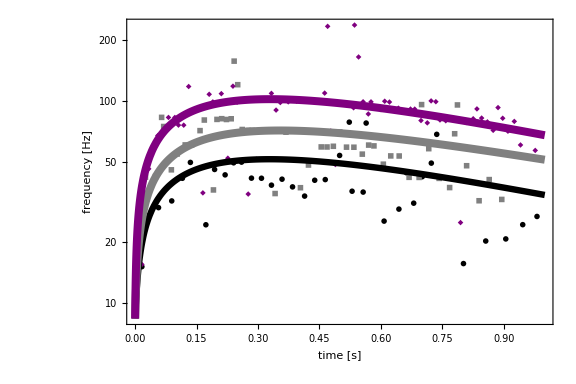

```mathematica
(*compare theoretical prediction for best fit parameters with the data from Bullock and Diecke*)FrequencyVsTimeFitPlotWithTaus=Show[ListLogPlot[{Sort[TimeSeriesFrequencyLongLower],Sort[TimeSeriesFrequencyLongMiddle],Sort[TimeSeriesFrequencyLong]},PlotStyle->{Black,Gray,Purple},PlotMarkers->{Automatic,Scaled[0.03]}],LogPlot[{FitTimeSeriesFreqCombined[1,t],FitTimeSeriesFreqCombined[2,t],FitTimeSeriesFreqCombined[3,t]},{t,0,1},PlotStyle->{{Black,Thickness[0.008]},{Gray,Thickness[0.01]},{ Purple,Thickness[0.01]}},PlotRange->All],PlotRange->All,
Frame->True,FrameLabel->{"time [s]","frequency [Hz]"},FrameStyle->Directive[22,Thick],ImageSize->Large,AspectRatio->2/3]
```

```mathematica
(*define inferred taus and best fit c*)
taus0=tausfit/.fitAlpha0Taus;
c0=c/.FitTimeSeriesFreqCombined["BestFitParameters"];
```

## Determine alpha values for comparison of interspike time distributions in simulation with data in Fig. 3

```mathematica
(*for the spontaneous background and for I=64, initial plateau, infer the corresponding alpha values and the change in the distance to the bifurcation with respect to the adapted state by matching the mean frequency; these values of alpha are used for the comparison in Fig. 5a*)DeltaTSpontaneous=DeltaT/.FindRoot[1/(taus0 m[c0 DeltaT+alpha0/.fitAlpha0Taus])==frequency,{DeltaT,0}]; 
AlphaSpontaneous=DeltaTSpontaneous*c0+alpha0/.fitAlpha0Taus;
(*for spontaneous background*)
DeltaTHighI=DeltaT/.FindRoot[1/(taus0 m[c0 DeltaT+alpha0/.fitAlpha0Taus])==frequencyhighI,{DeltaT,0}];
AlphaHighI = DeltaTHighI*c0+alpha0/.fitAlpha0Taus;
(*for I=64, initial plateau*)
```

```mathematica
(*values used in stochastic simulation*)
AlphaSpontaneous
AlphaHighI
```

0.16768

11.4801

## Fig. 5 (frequency as function of stimulus intensity)

```mathematica
(*determine mapping between temperature and intensity*)ScalingTemperatureIntensity=DeltaTHighI/64;
```

```mathematica
(*for the different preparations in Fig. 5 of Bullock and Diecke (different curves), import the data for frequency vs stimulus intensity (originally extracted with the help of WebPlotDigitizer)*)importFrequencyVsIntensity={{{1.01839,4.07141},{3.01108,12.1595},{16.1297,21.0904},{64.4364,36.1876},{265.726,53.2755}},{{1.01238,4.38045},{4.01666,7.36819},{16.0018,9.62714},{63.999,18.4944},{255.256,27.0548}},{{1.00214,5.98722},{4.00265,10.0703},{16.0895,16.4926},{64.0421,19.7653}},{{1.00506,7.96779},{2.00194,10.3338},{2.98786,10.9335},{4.00995,12.0496},{5.48924,13.0153}},{{1.00662,9.28374},{3.97157,17.3688},{16.0033,36.1348},{64.4547,71.759}},{{1.00757,10.189},{2.00505,12.0405},{3.96621,15.207},{7.9659,23.1319},{16.0552,49.7129}},{{1.00121,10.5339},{3.97371,18.3173},{16.0821,30.3988},{64.2247,50.4546}},{{1.01363,18.4084},{4.006,40.665},{15.9971,67.0469}}};
```

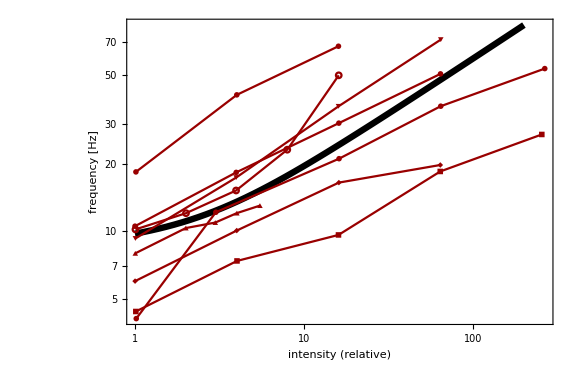

```mathematica
(*plot the data against the theoretical prediction*)
FrequencyVsIntensityComparisonPlot=Show[LogLogPlot[1/(taus0 m[c0 intensity ScalingTemperatureIntensity+alpha0/.fitAlpha0Taus]),{intensity,1,200},PlotStyle->{Black,Thickness[0.008]}],ListLogLogPlot[importFrequencyVsIntensity,Joined->True,PlotMarkers->{Automatic,Scaled[0.03]},PlotStyle->{{Darker[Red,0.4]}}],PlotRange->All,FrameLabel->{"intensity (relative)","frequency [Hz]"},Frame->True,Axes->None,FrameStyle->Directive[22,Thick],ImageSize->Large,AspectRatio-> 2/3]
```